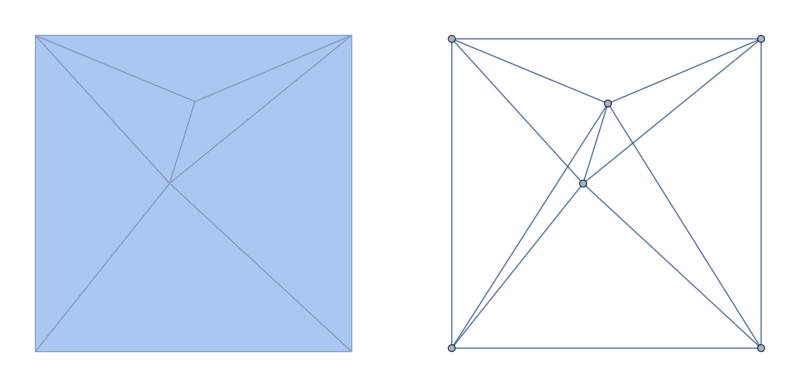

```mathematica
quadrilateral = {{-1,-1},{1,-1},{1,1},{-1,1}};
problem=quadrilateral;
AppendTo[problem,RandomReal[{-.85,.85},{1,2}][[1]]];
AppendTo[problem,RandomReal[{-.85,.85},{1,2}][[1]]];
delaunay=DelaunayMesh[problem];
connectivity={{0,1,0,1,1,1},{1,0,1,0,1,1},{0,1,0,1,1,1},{1,0,1,0,1,1},{1,1,1,1,0,1},{1,1,1,1,1,0}};
graph=AdjacencyGraph[connectivity,VertexCoordinates->problem];
GraphicsGrid[{{delaunay,graph}}]
```